```mathematica
io
```

io

```mathematica
Remove[io]
```

```mathematica
2+2
```

4

```mathematica
1+2+3
```

6

```mathematica
%*2
```

12

```mathematica
FactorInteger[12]
```

{{2,2},{3,1}}

```mathematica
((5-2)^(1+2))-2
```

25

```mathematica
GCD[2,3]
```

1

```mathematica
GCD[20, 72]
```

4

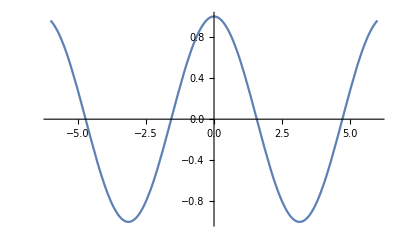

```mathematica
Plot[Evaluate[Cos[x]], {x, -6., 6.}]
```

```mathematica
{1,2,3}
{x,y,z}
```

{1,2,3}

{x,y,z}

```mathematica
%+2
```

{2+x,2+y,2+z}

```mathematica
%[2]
```

{2+x,2+y,2+z}[2]

```mathematica
{2+x,2+y,2+z}[[2]]
```

2+y

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
1/3+2/10
```

8/15

```mathematica
Together[2/35+10/298]
```

473/5215

```mathematica
.25+1/4
```

0.5

```mathematica
N[1/12+1/2]
```

0.583333

```mathematica
N[1/12+1/2, 4]
```

0.5833

```mathematica
ScientificForm[0.5833333333333333333`4.]
```

5.833×10^-1

```mathematica
ScientificForm[1/50]
```

1/50

```mathematica
N[100!]
```

9.33262×10^157

```mathematica
a2/b
```

a2/b

```mathematica
adag
```

adag

```mathematica
adag a
```

a adag

```mathematica
1+2^x./-> x = 5
```

```mathematica
1+2^x/. x->  5
```

33

```mathematica
x = %
```

33

```mathematica
x
```

33

```mathematica
Clear[x]
```

```mathematica
x
```

x

```mathematica
f[x_]:= 1+2x
```

```mathematica
f[5]
```

11

```mathematica
f[10]
```

21

```mathematica
Factor[x^2+2x+6]
```

6+2 x+x^2

```mathematica
FullSimplify[6+2 x+x^2]
```

6+x (2+x)

```mathematica
Expand[6+x (2+x)]
```

6+2 x+x^2

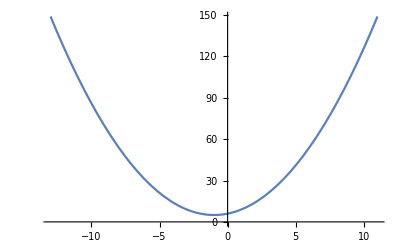

```mathematica
Plot[6+2 x+x^2,{x,-13.,11.}]
```

```mathematica
x = 2
```

2

```mathematica
x+2 == 4
```

True

```mathematica
1+z ==15
```

1+z==15

```mathematica
z
```

z

```mathematica
solve[x^2+ 2x+6]
```

solve[14]

```mathematica
solve[x^2+ 2x+6==0, x]
```

solve[False,2]

```mathematica
Solve[x^2+ 2x+6==0, x]
```

Solve::ivar: 2 is not a valid variable.

Solve[False,2]

```mathematica
Solve[x^2+ 5x+6==0, x]
```

Solve::ivar: 2 is not a valid variable.

Solve[False,2]

```mathematica
Solve[x^2+ 5x-6==0, x]
```

Solve::ivar: 2 is not a valid variable.

Solve[False,2]

```mathematica
Solve[x^2+5 x-6==0,x]
```

Solve::ivar: 2 is not a valid variable.

Solve[False,2]

```mathematica
x
```

2

```mathematica
Clear[x]
```

```mathematica
In[51]
```

{{x→-6},{x→1}}

```mathematica
In[50]
```

{{x→-6},{x→1}}

```mathematica
In[48]
```

{{x→-1-ⅈ √5},{x→-1+ⅈ √5}}

```mathematica
N[{{x->-1-ⅈ √5},{x->-1+ⅈ √5}}]
```

{{x→-1.-2.23607 ⅈ},{x→-1.+2.23607 ⅈ}}

```mathematica
NSolve[7 x^2+3x-5 == 0 ,x]
```

{{x→-1.08618},{x→0.657611}}

```mathematica
Solve[{x^2+5 ==y, 7x-5==y}, {x,y}]
```

{{x→2,y→9},{x→5,y→30}}

```mathematica
Roots[x^2+5x-6 ==0, x]
```

x==-6||x==1

```mathematica
Solve[x^2+5x-6 ==0,x]
```

{{x→-6},{x→1}}

```mathematica
NRoots[x^3+400 x^2-512x+2019]
```

NRoots::argtu: NRoots called with 1 argument; 2 or 3 arguments are expected.

NRoots[2019-512 x+400 x^2+x^3]

```mathematica
NRoots[2019-512 x+400 x^2+x^3==0, x]
```

x==-401.288||x==0.644214-2.14855 ⅈ||x==0.644214+2.14855 ⅈ

```mathematica
Reduce[{-2<x<10,-3≤ x≤4}, x]
```

-2<x≤4

```mathematica
Reduce[(x-3)(x-2)(x-6)<0,x]
```

x<2||3<x<6

```mathematica
(x-3)(x-2)(x-6)
```

(-6+x) (-3+x) (-2+x)

```mathematica
Expand[(-6+x) (-3+x) (-2+x)]
```

-36+36 x-11 x^2+x^3

```mathematica
Solve[-36+36 x-11 x^2+x^3 ==0,x]
```

{{x→2},{x→3},{x→6}}

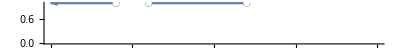

```mathematica
NumberLinePlot[x<2||3<x<6, {x, 0, 10}]
```

```mathematica
FormulaData["QuadraticEquation"]
```

c MultiplicativeConstants+b MultiplicativeConstants x MultiplicativeConstants+a MultiplicativeConstants (x MultiplicativeConstants)^2==0

WolframAlphaQueryResults

x^2-2 x+1==0
a x^2+b x+c==0 | 
x | indeterminate variable
a | quadratic coefficient
b | linear coefficient
c | constant coefficient
(x==(-b±√(b^2-4 a c))/(2 a))

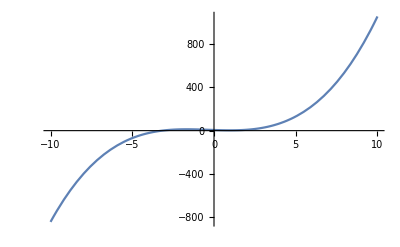

```mathematica
Plot[x^3+x^2-5x+6, {x,-10,10}]
```

```mathematica
Reduce[{x^2+6y<3&&y>0}]
```

0<y<1/2&&-√(3-6 y)<x<√(3-6 y)

```mathematica
RegionPlot[%, {x,-3,3},{y,-10,10}]
```

-Graphics-

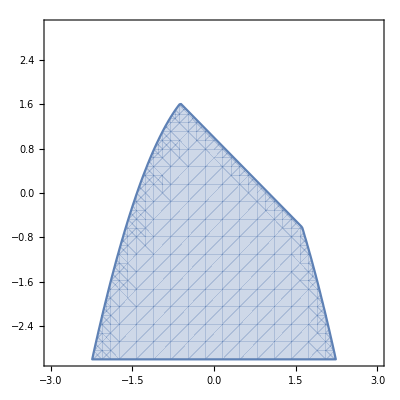

```mathematica
RegionPlot[Reduce[{x^2 + y < 2 && x + y < 1}], {x, -3, 3}, {y, -3, 3}]
```

```mathematica
Reduce[{x^2 + y < 2 && x + y < 1}]
```

(x≤1/2 (1-√5)&&y<2-x^2)||(1/2 (1-√5)<x≤1/2 (1+√5)&&y<1-x)||(x>1/2 (1+√5)&&y<2-x^2)

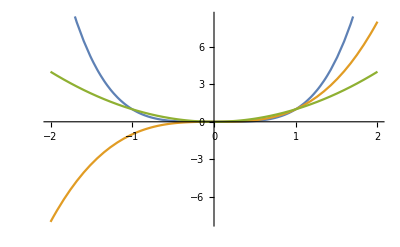

```mathematica
Plot[{x^4, x^3, x^2}, {x,-2,2}, PlotLegends -> Expression]
```

```mathematica
Plot[{x^4, x^3, x^2}, {x,-2,2}, PlotLegends -> "Expression"]
```

-Graphics-

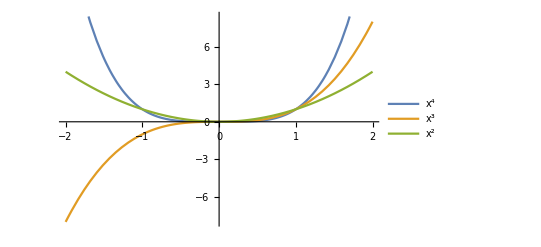

```mathematica
Plot[{x^4, x^3, x^2}, {x,-2,2}, PlotLegends -> "Expressions"]
```

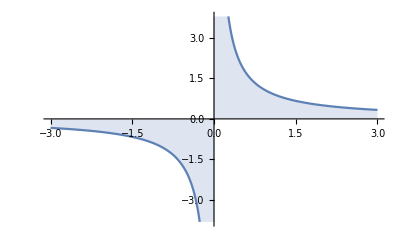

```mathematica
Plot[1/x,{x,-3,3}, Filling->Axis]
```

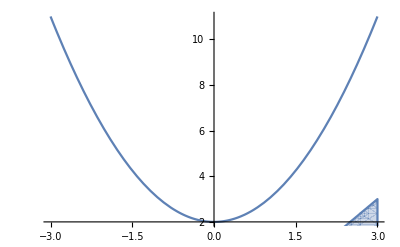

```mathematica
Show[{Plot[x^2+2, {x,-3,3}],RegionPlot[2x>y+3,{x,-3,3},{y,0,9}]}]
```

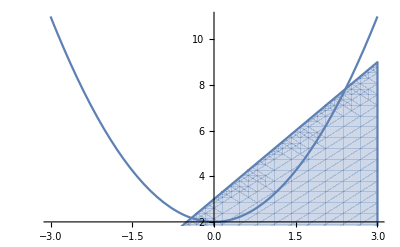

```mathematica
Show[{Plot[x^2+2, {x,-3,3}],RegionPlot[2x>y-3,{x,-3,3},{y,0,9}]}]
```

```mathematica
Graphics[Disk]
```

-Graphics-



```mathematica
Graphics[Disk[]]
```

```mathematica
Graphics[Rectangle[10,-10,10]]
```

First::normal: Nonatomic expression expected at position 1 in First[System`Dump`$2DComplex].

-Graphics-

```mathematica
Graphics[Rectangle[{-2,-2},{10,10}]
```



```mathematica
Graphics[Rectangle[{-2,-2},{10,10}]]
```

```mathematica
Graphics[{Green, Rectangle[{0,2},{-4,-4}], Red, Disk[]]
```

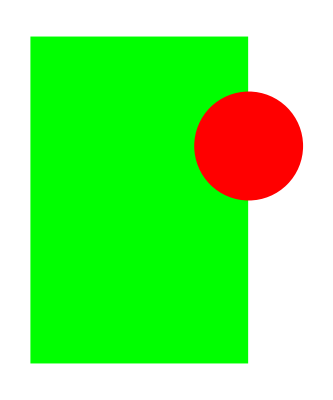

```mathematica
Graphics[{Green, Rectangle[{0,2},{-4,-4}], Red, Disk[]}]
```

```mathematica
tr = SASTriangle[10, 90°, 10]
```

Triangle[{{0,0},{10 √2,0},{5 √2,5 √2}}]

```mathematica
Graphics[Tr], Area[Tr]
```

Syntax::tsntxi: "Graphics[Tr],Area[Tr]" is incomplete; more input is needed.

```mathematica
Graphics[Tr] Area[Tr]
```

Area[Tr] -Graphics-

```mathematica
Graphics[Tr]
```

-Graphics-

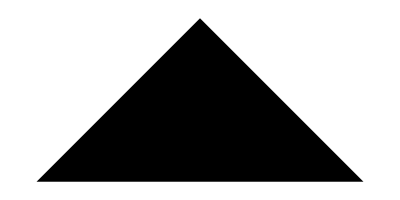

```mathematica
Graphics[tr]
```

```mathematica
Area[tr]
```

50

```mathematica
Graphics3D[Ball[]]
```

-Graphics3D-

```mathematica
Volume[Cylinder[]]
```

2 π

```mathematica
Entity["Solid","SolidCylinder"][EntityProperty["Solid","Volume"]]
```

```mathematica
Function[{a,h},π a^2 h]
```

Function[{a,h},π a^2 h]

WolframAlphaQueryResults

V==π a^2 h
(for a circular right cylinder with center at the origin, height h, radius a)

```mathematica
Graphics[Rotate[Rectangle[],45°]]
```

-Graphics-

```mathematica
Sin[x]/Cos[x]
```

Tan[x]

```mathematica
ArcTan[1]
```

π/4

```mathematica
Sin[π/2]
```

1

```mathematica
Sin[90°]
```

1

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

```mathematica
TrigFactor[cos[x]^3]
```

cos[x]^3

```mathematica
TrigFactor[cos[x]^2-sin[x]^3]
```

cos[x]^2-sin[x]^3

```mathematica
TrigFactor[Cos[x]^2-Sin[x]^4]
```

1/8 (1+8 Cos[2 x]-Cos[4 x])

```mathematica
Solve[Cos[x]^2+Sin[x]^2==x]
```

{{x→1}}

```mathematica
Solve[{Tan[x]==1, 0<x<2pi}]
```

{{x→ConditionalExpression[1/4 (π+4 π C[1]), C[1]∈ℤ&&C[1]≥0&&pi>1/8 (π+4 π C[1])]}}

```mathematica
Solve[{Tan[x]==1,0<x<2 Pi}]
```

{{x→π/4},{x→(5 π)/4}}

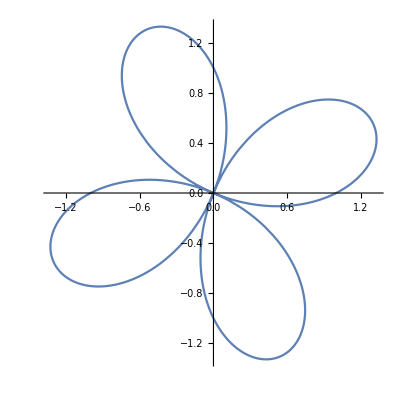

```mathematica
PolarPlot[Sin[2θ]+Cos[2θ], {θ, 0, 2 π}]
```

```mathematica
PolarPlot[Sin[2θ]+Cos[2θ], {θ, 0, 2 π}, PolarAxes -> Automatic, PolarTicks -> {0°, 90°, 180°, 270deg}]
```

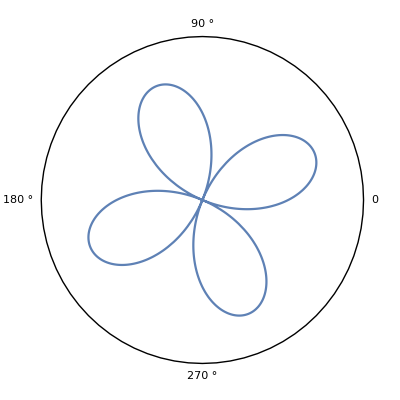

```mathematica
PolarPlot[Sin[2θ]+Cos[2θ], {θ, 0, 2 π}, PolarAxes -> Automatic, PolarTicks -> {0°, 90°, 180°, 270°}]
```

```mathematica
PolarPlot[Sin[2 θ]+Cos[2 θ],{θ,0,2 Pi},PolarAxes->Automatic,PolarTicks->{0 °,90 °,180 °,270 °}]
```

-Graphics-

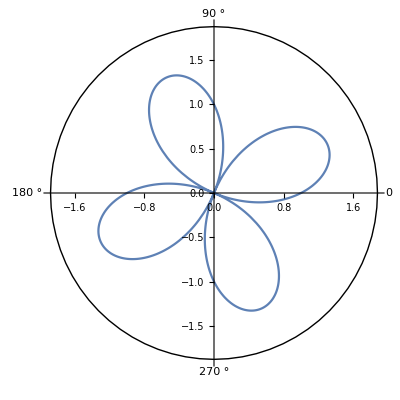

```mathematica
Show[%3,Axes->True]
```

```mathematica
ToPolarCoordinates[1,1]
```

ToPolarCoordinates::argx: ToPolarCoordinates called with 2 arguments; 1 argument is expected.

ToPolarCoordinates[1,1]

```mathematica
ToPolarCoordinates[{1,1}]
```

{√2,π/4}

```mathematica
Log[E^2]
```

2

```mathematica
Log[2, 64]
```

6

```mathematica
Log[10,10000000]
```

7

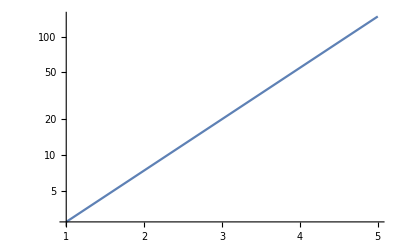

```mathematica
LogPlot[Exp[x], {x, 1, 5}]
```

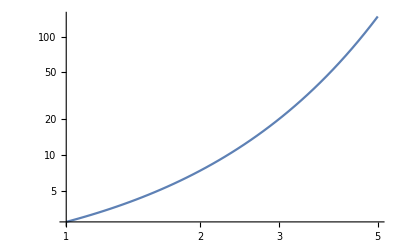

```mathematica
LogLogPlot[E^x, {x,1,5}]
```

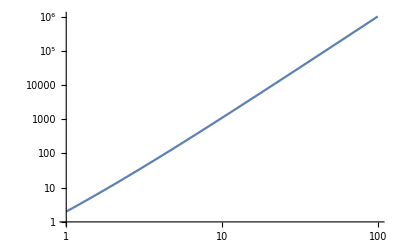

```mathematica
LogLogPlot[x^2 + x^3, {x, 1, 100}]
```

```mathematica
Limit[(x^6+1)/(x^3-1), x->1]
```

Indeterminate

```mathematica
Limit[(x^3-1)/(x-1),x->1]
```

3

```mathematica
Limit[Sin[x]/x, x-> 1]
```

Sin[1]

```mathematica
Limit[Sin[x]/x, x-> 0]
```

1

```mathematica
Limit[(2 x^3-1)/(5 x^3+x-1),x->∞]
```

2/5

```mathematica
Limit[1/x, x-> 0, Direction -> 1]
```

-∞

```mathematica
lim_(x->0^-) 1/x
```

-∞

```mathematica
Limit[1/x, x->0, Direction -> -1]
```

∞

```mathematica
TraditionalForm[HoldForm[Limit[Sin[x]/x, x->0]]]
```

(sin(x))/xx0

```mathematica
D[x^6, x]
```

6 x^5

```mathematica
D[x^6, {x,4}]
```

360 x^2

```mathematica
Sin'[x]
```

Cos[x]

```mathematica
Sin''''[4x]
```

Sin[4 x]

```mathematica
Sin'[3x]
```

Cos[3 x]

```mathematica
D[Sin[3x],x]
```

3 Cos[3 x]

```mathematica
Sin[3x]'
```

Sin[3 x]'

```mathematica
[Sin[3x]]'
```

Syntax::sntxb: Expression cannot begin with "[Sin[3x]]'".

```mathematica
f[x_]:= x^2+2x+6
```

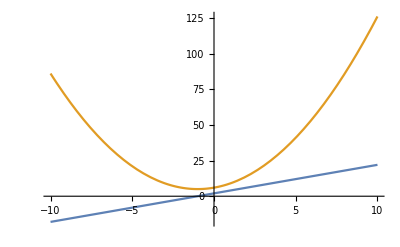

```mathematica
Plot[{f'[x], f[x]}, {x, -10, 10}]
```

```mathematica
D[x^10, {x, 10}]
```

3628800

WolframAlphaQueryResults

{{formalisation,Noun}→the act of making formal (as by stating formal rules governing classes of expressions)}

WolframAlphaQueryParseResults

{d/dx(f(x) g(x)) == f(x) g'(x) + g(x) f'(x)}

```mathematica
Integrate[8 x^5, x]
```

(4 x^6)/3

```mathematica
∫8 x^4 dx
```

Integrate::nodiffd: ∫8 x^4 dx cannot be interpreted. Integrals are entered in the form ∫fⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

```mathematica
∫8 x^4 ⅆx
```

(8 x^5)/5

```mathematica
∫3y6x^3ⅆxⅆy
```

Integrate::intnest: The integral ∫3y6x^3ⅆxⅆy cannot be interpreted. The number of definite and indefinite integral operators must match the number of differential operators.

```mathematica
∫1∫3 xy^(2x)ⅆxⅆy
```

Integrate::intnest: The integral ∫3 xy^(2x)ⅆxⅆy cannot be interpreted. The number of definite and indefinite integral operators must match the number of differential operators.

```mathematica
∫1∫3 xy^2 ⅆxⅆy
```

Integrate::intnest: The integral ∫3 xy^2 ⅆxⅆy cannot be interpreted. The number of definite and indefinite integral operators must match the number of differential operators.

```mathematica
∫1[∫3 xy^2 ⅆx]ⅆy
```

y 1[3 x xy^2]

```mathematica
∫∫3 xy^2 ⅆxⅆy
```

3 x xy^2 y

```mathematica
Integrate[3 xy^2, x]
```

3 x xy^2

```mathematica
Integrate[3x y^2, x]
```

(3 x^2 y^2)/2

```mathematica
∫∫3x y^2 ⅆxⅆy
```

(x^2 y^3)/2

```mathematica
∫_0^π Sin[x]ⅆx
```

2

```mathematica
NIntegrate[ x^3 Sin[x] + 2 Log[3x]^2, {x, 0, π}]
```

28.1531

```mathematica
Fibonacci[x]
```

Fibonacci[x]

```mathematica
Fibonacci[4]
```

3

```mathematica
Table[x^2, x]
```

Table::nliter: Non-list iterator x at position 2 does not evaluate to a real numeric value.

Table[x^2,x]

```mathematica
Table[x^2,x, 0]
```

Table::nliter: Non-list iterator x at position 2 does not evaluate to a real numeric value.

Table[x^2,x,0]

```mathematica
Table[x^3, x, 10]
```

Table::nliter: Non-list iterator x at position 2 does not evaluate to a real numeric value.

Table[x^3,x,10]

```mathematica
Table[x^3, 0, 10]
```

{}

```mathematica
Table[x^3, {x, 0, 10}]
```

{0,1,8,27,64,125,216,343,512,729,1000}

```mathematica
Table[Fibonacci[x], {x, 0, 10}]
```

{0,1,1,2,3,5,8,13,21,34,55}

```mathematica
RecurrenceTable[{a[x]==2a[x-1], a[1]=2, {x,1,8}]
```

```mathematica
RecurrenceTable[{a[x]==2a[x-1]}, a[1]=2, {x,1,8}]
```

RecurrenceTable::dsfun: 2 cannot be used as a function.

RecurrenceTable[{a[x]==2 a[-1+x]},2,{x,1,8}]

```mathematica
RecurrenceTable[{a[x]==2a[x-1]}, a[1]==2, {x,1,8}]
```

RecurrenceTable::ivar: True is not a valid variable.

RecurrenceTable[{a[x]==2 a[-1+x]},True,{x,1,8}]

```mathematica
RecurrenceTable[{a[x]==2a[x-1]}, a[1]==1, {x,1,8}]
```

RecurrenceTable::ivar: False is not a valid variable.

RecurrenceTable[{a[x]==2 a[-1+x]},False,{x,1,8}]

```mathematica
RecurrenceTable[{a[x]==2a[x-1]}, a[1]==1, a, {x,1,8}]
```

RecurrenceTable::ivar: False is not a valid variable.

RecurrenceTable[{a[x]==2 a[-1+x]},False,a,{x,1,8}]

```mathematica
RecurrenceTable[{a[x]==2a[x-1], a[1]==1}, a, {x,1,8}]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of False in the first argument {a[x]==2 a[-1+x],False}.

RecurrenceTable[{a[x]==2 a[-1+x],False},a,{x,1,8}]

```mathematica
RecurrenceTable[{a [x]==2a [x-1], a[1]==1}, a, {x,1,8}]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of False in the first argument {a[x]==2 a[-1+x],False}.

RecurrenceTable[{a[x]==2 a[-1+x],False},a,{x,1,8}]

```mathematica
RecurrenceTable[{a[x]==2 a[x-1],a[1]==1},a,{x,1,8}]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of False in the first argument {a[x]==2 a[-1+x],False}.

```mathematica
RecurrenceTable[{a[x]==2 a[-1+x],False},a,{x,1,8}]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of False in the first argument {a[x]==2 a[-1+x],False}.

RecurrenceTable[{a[x]==2 a[-1+x],False},a,{x,1,8}]

```mathematica
RecurrenceTable[{a[x]==2 a[-1+x],False},a,{x,1,8}]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of False in the first argument {a[x]==2 a[-1+x],False}.

RecurrenceTable[{a[x]==2 a[-1+x],False},a,{x,1,8}]

```mathematica
RecurrenceTable[{a[n+1]==3a[n],a[1]==7},a,{n,1,10}]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of False in the first argument {a[1+n]==3 a[n],False}.

RecurrenceTable[{a[1+n]==3 a[n],False},a,{n,1,10}]

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAll
```

ClearAll

```mathematica
In[62]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of False in the first argument {a[1+n]==3 a[n],False}.

RecurrenceTable[{a[1+n]==3 a[n],False},a,{n,1,10}]

```mathematica
RecurrenceTable[{a[1+n]==3 a[n],False},a,{n,1,10}]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of False in the first argument {a[1+n]==3 a[n],False}.

RecurrenceTable[{a[1+n]==3 a[n],False},a,{n,1,10}]

```mathematica
Clear[a]
```

```mathematica
Clear[n]
```

```mathematica
RecurrenceTable[{a[x] == 2 a[x - 1], a[1] == 1}, a, {x, 1, 8}]
```

{1,2,4,8,16,32,64,128}

```mathematica
Total[%]
```

255

```mathematica
Sum[i (i+1), {i, 1, 10}]
```

440

```mathematica
∑_(i=0)^10 i (i+1)
```

440

```mathematica
∑_(i=1)^n ∑_(j=1)^n i j
```

1/4 n^2 (1+n)^2

```mathematica
FindSequenceFunction[{2,4,6,8}, n]
```

2 n

```mathematica
FindSequenceFunction[{2,10,18}, n]
```

FindSequenceFunction[{2,10,18},n]

```mathematica
FindSequenceFunction[{8,16,24},n]
```

```mathematica
FindSequenceFunction[{8,16,24, 32},n]
```

8 n

```mathematica
FindSequenceFunction[{10,18,26, 34},n]
```

2 (1+4 n)

```mathematica
Series[Exp[x^2],{x, 0, 8}]
```

1+x^2+x^4/2+x^6/6+x^8/24+O[x]^9

```mathematica
Normal[1+x^2+x^4/2+x^6/6+x^8/24+O[x]^9]
```

1+x^2+x^4/2+x^6/6+x^8/24

```mathematica
Series[Exp[Sin[x]], {x, 0, 8}]
```

1+x+x^2/2-x^4/8-x^5/15-x^6/240+x^7/90+(31 x^8)/5760+O[x]^9

```mathematica
Series[2 f[x] -3 {x,0,3}]
```

Series::argmu: Series called with 1 argument; 2 or more arguments are expected.

Series[{-3 x+2 (6+2 x+x^2),2 (6+2 x+x^2),-9+2 (6+2 x+x^2)}]

```mathematica
Series[2 f[x] -3, {x,0,3}]
```

9+4 x+2 x^2+O[x]^4

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAll
```

ClearAll

```mathematica
IN[83]
```

IN[83]

```mathematica
In[83[
```

```mathematica
In[83]
```

9+4 x+2 x^2+O[x]^4

```mathematica
Series[2 f[x] -3, {x,0,3}]
```

9+4 x+2 x^2+O[x]^4

```mathematica
f[x]
```

6+2 x+x^2

```mathematica
Clear[f[x]]
```

Clear::ssym: f[x] is not a symbol or a string.

```mathematica
Clear[f]
```

```mathematica
f[x]
```

f[x]

```mathematica
In[83]
```

(-3+2 f[0])+2 f'[0] x+f''[0] x^2+1/3 f^(3)[0] x^3+O[x]^4

```mathematica
∑_(n=0)^∞ (1/2)^n
```

2